# Onset of Chaos

## Lab 11

Kym Derriman

## Enter section title here

### Enter subsection title here

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
∫xⅆx+√z
```

x^2/2+√z

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}

## Introduction

### Enter subsection title here

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
∫xⅆx+√z
```

x^2/2+√z

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}

## Background

### Enter subsection title here

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
∫xⅆx+√z
```

x^2/2+√z

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}

## The Logistic Map

### Description

xyz

#### The Logistic Equation

The logistic equation describes a growth model. I’ve seen it described in the same terms as a population growth equation. There’s the “growth factor,” a, and the “ceiling” factor (1-x) that puts a cap on how much the population (or whatever) can grow.

x_(n+1)=a x_n (1-x_n)

The Mathematica function is defined below.

```mathematica
logisticStep[x_,a_]:=a x (1-x)
```

Test this function to show one step.

```mathematica
logisticStep[0.5,2.8]
```

0.7

#### The Logistic Iteration

To create the map itself, we apply the logistic equation repeatedly. For this, NestList[] is used to iterate.

```mathematica
logisticIteration[x0_,a_,n_]:=NestList[logisticStep[#,a]&,x0,n]
```

And we can test this with some arbitrary parameters.

```mathematica
logisticIteration[0.5,2.8,10]//Column//Framed
```

0.5
0.7
0.588
0.678317
0.610969
0.665521
0.623288
0.65744
0.630595
0.652246
0.6351

We see that these values are converging around a value of 0.64. The following parameters give the expectation of convergence depending on the value of the growth factor, a.

Decay to zero: 0<a<1

Convergence to a specific value: 1<a<3

Oscillation around a specific value: 3<a< ~3.57

Chaotic behavior: ~3.57<a

The functions defined above allow plotting of the logistic map to observe the behavior of the system. The logistic map is first examined by plotting values of a with random values of x_0 such that 0<x_0<1.

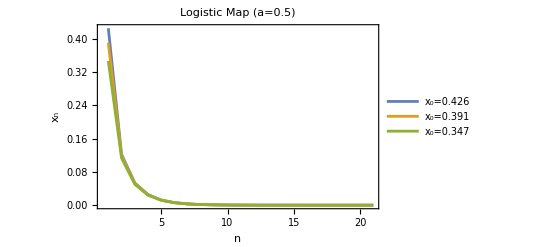
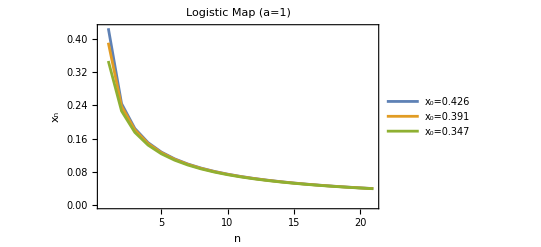
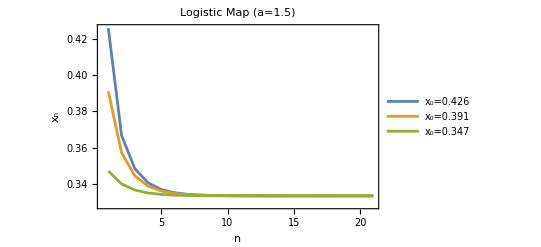
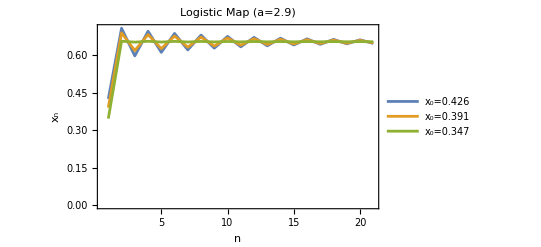
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
plotLogisticMap[a_,initialConditions_]:= Module[{data,plots},
data=Table[
logisticIteration[x0,a,20],
{x0,initialConditions}
];
ListLinePlot[data,
PlotRange->All,
Frame->True,
FrameLabel->{"n","x_n"},
PlotLegends->Map[
StringForm["x_0=``",NumberForm[#,{4,3}]]&,
initialConditions
],
PlotLabel->StringForm["Logistic Map (a=``)",a]
]
]

(*Generate 3 random initial conditions between 0 and 1*)
SeedRandom[42];  (*for reproducibility*)
initialConditions=RandomReal[{0,1},3];

(*Create plots for each value of a*)
aValues={0.5,1,1.5,2.9};
plots=Map[plotLogisticMap[#,initialConditions]&,aValues];

(*Display plots in a grid*)
Grid[Partition[plots,2]]
```